```mathematica
$PlotTheme="Scientific";
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xfrac}"}];
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

```mathematica
ctdfracterms=20;
```

```mathematica
Z[s_]:=Which[Im[s]≥1,ContinuedFractionK[If[n==1,s,-1/2 (-1+n) (-3+2 n)],-s^2-3/2+2 n,{n,1,ctdfracterms}],-1<Im[s]<1,ⅈ*√π*Exp[-s^2]*(1+Erf[ⅈ*s]),Im[s]≤-1,2*ⅈ*√π*Exp[-s^2]+Conjugate[ContinuedFractionK[If[n==1,Conjugate[s],-1/2 (-1+n) (-3+2 n)],-Conjugate[s]^2-3/2+2 n,{n,1,ctdfracterms}]],True,"Error"]
```

```mathematica
P[k_,ω_]:=1+ω/(√2*k)*Z[ω/(√2*k)]
```

```mathematica
argand[tab_,b__]:=ListPlot[Transpose[{Re[tab],Im[tab]}],FrameLabel->{MaTeX["\\sfrac{\\text{Re}[\\omega]}{k_\\text{J}\\sigma}",Magnification->1.25],MaTeX["\\sfrac{\\text{Im}[\\omega]}{k_\\text{J}\\sigma}",Magnification->1.25]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,AspectRatio->Automatic,b]
```

```mathematica
solnneg[k_,start_]:=FindRoot[P[k,ω]==k^2,{ω,start*(1-ⅈ)}][[1,2]]
```

```mathematica
zeroes[k_,begin_,end_,dp_]:=SortBy[DeleteDuplicatesBy[Cases[Table[If[Abs[P[k,res=solnneg[k,start]]-k^2]<=10^-dp,Chop[res]],{start,begin,end,10^-dp}],Except[Null]],(Round[#,10^-dp])&],Re]
```

```mathematica
res1=zeroes[0.1,0.1,2.5,4];
```

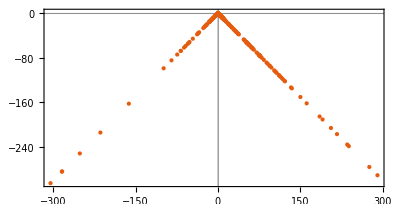

```mathematica
arg1=argand[res1,PlotRange->{{-0.05,1.05},{0.05,-1.05}},GridLines->{Range[0,1,0.2],Range[0,-1,-0.2]},PlotStyle->(psarg={colors[[1]],PointSize[Medium]})]
```

```mathematica
res2=zeroes[0.01,0.01,0.25,5];
```

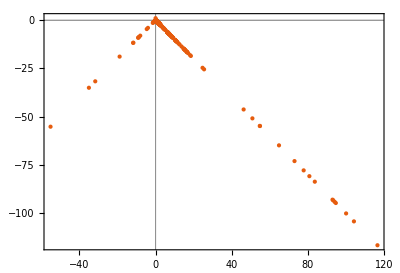

```mathematica
arg2=argand[res2,PlotRange->{{-0.005,0.105},{0.005,-0.105}},GridLines->{Range[0,0.1,0.02],Range[0,-0.1,-0.02]},PlotStyle->psarg]
```

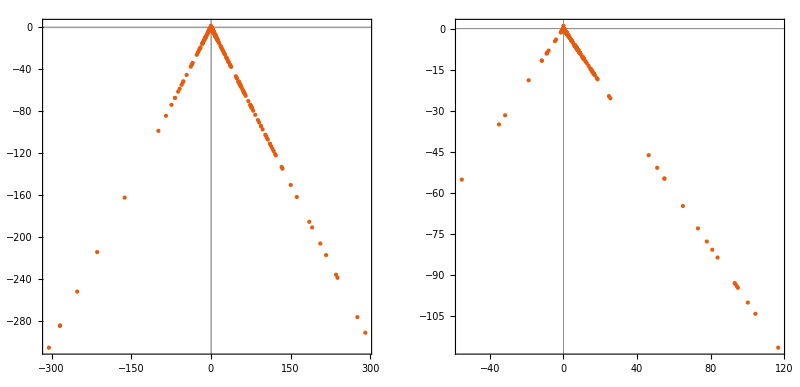

```mathematica
arg12=GraphicsRow[{arg1,arg2},ImageSize->Full]
```

```mathematica
Export["figarg1.pdf",arg1];
```

```mathematica
Export["figarg2.pdf",arg2];
```

```mathematica
Solve[ω==2*σ*k*√(π*(n-1/8)),n]
```

{{n→(k^2 π σ^2+2 ω^2)/(8 k^2 π σ^2)}}

```mathematica
nofω[k_,ω_]:=Floor[(k^2 π+2 ω^2)/(8 k^2 π)]
```

```mathematica
nofωdiff[k_,ω1_,ω2_]:=nofω[k,ω2]-nofω[k,ω1]
```

The next line was originally used to calculate zeros for k=0.01 k_J...

```mathematica
(*res1abs=zeroes[0.1,9/(√2),12/(√2),4];Export["k01kJzeros.m",res1abs];*)
```

...but it can also be more quickly imported using the next line

```mathematica
res1abs=<<"k01kJzeros.m";
```

```mathematica
disp10[ω_]:=Abs[10^-2-P[10^-1,ω]]
```

```mathematica
MaximalBy[res1abs,disp10]
```

{-36.527-36.5237 ⅈ}

```mathematica
disp10[-36.52695721675392-36.52373444840748 ⅈ]
```

1.04298×10^-8

```mathematica
Count[res1abs,u_/;10<Abs[u]<11]
```

168

```mathematica
nofωdiff[0.1,10,11]
```

168

```mathematica
res1absrange=Cases[res1abs,u_/;10<Abs[u]<11];
```

```mathematica
formuladeviation[k_]:=k^2/10^2*Log[(√(2*π)*10/2)/k^3]
```

1.0128×10^-3

```mathematica
deviationfromdiagonal1=ScientificForm[(Arg[MaximalBy[res1absrange,Arg]][[1]]-(-π/4)),20]
```

1.012796820577311×10^-3

```mathematica
ScientificForm[(Arg[SortBy[res1absrange,Abs][[1]]]-(-π/4)),20]
```

1.012796820577311×10^-3

```mathematica
formuladeviation[0.1]//ScientificForm
```

9.43613×10^-4

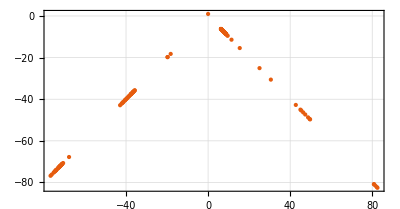

```mathematica
arg1abs=argand[res1abs,PlotRange->{{9/(√2),12/(√2)},{-9/(√2),-12/(√2)}},GridLines->Automatic,PlotStyle->(psarg={colors[[1]],PointSize[Medium]}),PlotLabel->MaTeX["k=0.1 k_\\text{J}",Magnification->1.25]]
```

The next line was originally used to calculate zeros for k=0.01 k_J...

```mathematica
(*res2abs=zeroes[0.01,9/(√2),12/(√2),5];Export["k001kJzeros.m",res2abs];*)
```

...but it can also be more quickly imported using the next line

```mathematica
res2abs=<<"k001kJzeros.m";
```

```mathematica
disp100[ω_]:=Abs[10^-4-P[10^-2,ω]]
```

```mathematica
MaximalBy[res2abs,disp100]
```

{8.00104-8.00082 ⅈ}

```mathematica
disp100[8.001038380632021-8.000823899480851 ⅈ]
```

1.05345×10^-8

```mathematica
Count[res2abs,u_/;10<Abs[u]<11]
```

16712

```mathematica
nofωdiff[0.01,10,11]
```

16711

```mathematica
res2absrange=Cases[res2abs,u_/;10<Abs[u]<11];
```

```mathematica
deviationfromdiagonal2=ScientificForm[(Arg[MaximalBy[res2absrange,Arg]][[1]]-(-π/4)),20]
```

1.703690119381207×10^-5

```mathematica
ScientificForm[(Arg[SortBy[res2absrange,Abs][[1]]]-(-π/4)),20]
```

1.703690119381207×10^-5

```mathematica
formuladeviation[0.01]//ScientificForm
```

1.63439×10^-5

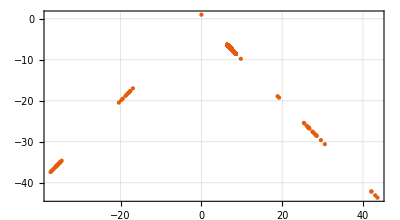

```mathematica
arg2abs=argand[res2abs,PlotRange->{{9/(√2),12/(√2)},{-9/(√2),-12/(√2)}},GridLines->Automatic,PlotStyle->(psarg={colors[[1]],PointSize[Medium]}),PlotLabel->MaTeX["k=0.1 k_\\text{J}",Magnification->1.25]]
```